{4→0,5→1,6→2,7→3,8→4,9→5,10→6,11→7,12→8,13→9,14→10,15→11,17→12,18→13,19→14,20→15,24→16,25→17,26→18}

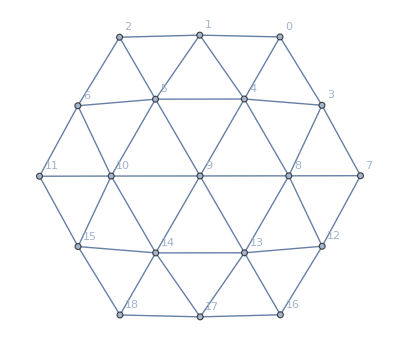

triangularHexagonGrid.graphml

```mathematica
G = GraphData[{"TriangularHoneycombKing",7}];
Graph[G, VertexLabels->"Name"];
K = VertexDelete[G, {1,2,3, 22,16,23,28,21,27}];
coordinates = Map[(First[#]-> Part[#,2]&),Transpose[{VertexList[K],Range[0, VertexCount[K]-1]}]]
H = VertexReplace[K, coordinates];
Graph[H, VertexLabels->"Name"]
Export["triangularHexagonGrid.graphml", H]
```